# Multi Grid PDE

Partial Differential Equations (PDEs) can be approximated at different resolutions.  The finer detail that can be revealed at higher resolution usually introduce poorly conditioned matrices. Multigrid schemes use different resolutions to precondition iterative solvers.

We are going to look at this in the simplest possible case 
	u_xx=f and u(0)=u(1)=0
with the standard 
	u_xx≈(u(x_(i-1))-2u(x_i)+u(x_(i+1)))/Δx^2
discretization.  This is the 1;-2;1 discretization we looked at before.  We need to include the scaling to “match” the two different scales of discretization.

```mathematica
n=32;
AFull=SparseArray[{Band[{1,1}]->-2.0,Band[{2,1}]->1.0,Band[{1,2}]->1.0},{2n,2 n}];
AHalf=AFull⟦1;;n,1;;n⟧;
TabView[{
"ATop"->MatrixForm[AFull⟦1;;12,1;;12⟧],
"Evals"->ListLogPlot[ Map[Eigenvalues,{-AFull, -AHalf}]]
},2]
```

12

## Multi Grid

This is going to look a bit strange but I am going to build two operators that map between the grids.
The first is an interpolation operator from the coarse grid to the fine grid.  The second is a restriction operator from the fine grid to the coarse grid. Neither is represented by a square matrix!

### Restriction Operator

The restriction operator maps the fine discretization onto coarse discretization.  We need to work out why it is appropriate to call this a restriction operator and why it could look something like this.

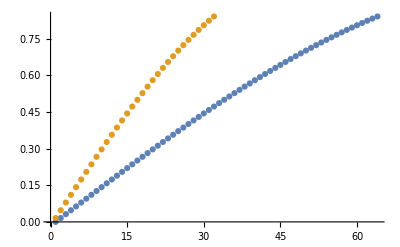

```mathematica
BRestrict=SparseArray[{},{n,2n}];
Do[BRestrict⟦i,2i⟧=1.0,{i,1,n}];
Δx=1.0/(2n-1);
uFine=Table[Sin[x],{x,0,1,Δx}];
ListPlot[{uFine,BRestrict.uFine}]
```

### Interpolation Operator

The interpolation operator maps the coarse discretization onto the fine discretization.  We need to work out why it is appropriate to call this an interpolation operator and why it could look something like this. We can easily make this better.

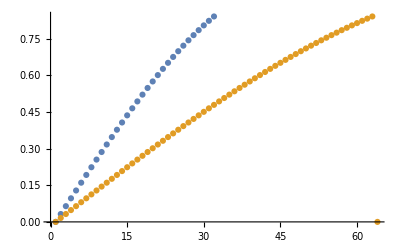

```mathematica
BInterp=SparseArray[{},{2n,n}];
Do[
BInterp⟦2i-1,i⟧=1.0,
{i,1,n}];
Do[
BInterp⟦i,i/2⟧=0.5;
BInterp⟦i,1+i/2⟧=0.5,
{i,2,2n-1,2}];
Δx=1.0/(n-1);
uCoarse=Table[Sin[x],{x,0,1,Δx}];
ListPlot[{uCoarse,BInterp.uCoarse}]
```

### Multi Grid Scheme

Use the coarse grid solver as a preconditioner for the fine grid which is what you really care about.   This area has a lot of jargon and a lot of detailed implementation. We will come back to it probably in way too much detail!   Just as a teaser,  most multi-grid schemes use three levels!

### Algebraic Multi Grid

There is a collection of techniques called Algebraic Multigrid (AMG) that attempt to apply multigrid ideas of reducing the dimension to get a smaller problem without using any notion of grid.  Essentially the smaller problem is used as a preconditioner for the original problem.   Terminology and jargon persist. The small problem is the coarse problem and the top level iteration is a “smoother”.  Again we will come back to this but we want to make sure we try to at least mention as many flavors of preconditioners as we can.